```mathematica
q[x_, l_] := Module[{a = 1/(2(1+2 Log10[l])),w = (1/(2(1+2 Log10[l])))^(-1/l)},+Piecewise[{{0,x≤ a},{1 + Floor[Log10[x/a]/Log10[w]],a<x≤ 1},{l +1 + Floor[(Log10[a x] + (l* Log10[w]))/Log10[w]],1<x≤ 1/a},{2 l + 1,x>1/a}}] ]
```

```mathematica
Manipulate[Plot[q[x,l],{x,0,6},AxesLabel->{"Price Relative","Integer"}],{l,1,10}]
```

```mathematica
DynamicModule[{l=4.},Plot[q[x,l],{x,0,6},AxesLabel->{"Price Relative","Integer"}]]
```

Cell[BoxData[

 TagBox[

  StyleBox[

   DynamicModuleBox[{$CellContext`l$$ = 8 $CellContext`\[AliasDelimiter], 

    Typeset`show$$ = True, Typeset`bookmarkList$$ = {}, 

    Typeset`bookmarkMode$$ = "Menu", Typeset`animator$$, Typeset`animvar$$ = 

    1, Typeset`name$$ = "\"untitled\"", Typeset`specs$$ = {{

      Hold[$CellContext`l$$], 1, 10}}, Typeset`size$$ = {885., {270., 273.}}, 

    Typeset`update$$ = 0, Typeset`initDone$$, Typeset`skipInitDone$$ = 

    True, $CellContext`l$1320$$ = 0}, 

    DynamicBox[Manipulate`ManipulateBoxes[

     1, StandardForm, "Variables" :> {$CellContext`l$$ = 1}, 

      "ControllerVariables" :> {

        Hold[$CellContext`l$$, $CellContext`l$1320$$, 0]}, 

      "OtherVariables" :> {

       Typeset`show$$, Typeset`bookmarkList$$, Typeset`bookmarkMode$$, 

        Typeset`animator$$, Typeset`animvar$$, Typeset`name$$, 

        Typeset`specs$$, Typeset`size$$, Typeset`update$$, Typeset`initDone$$,

         Typeset`skipInitDone$$}, "Body" :> Plot[

        $CellContext`q[$CellContext`x, $CellContext`l$$], {$CellContext`x, 0, 

         6}], "Specifications" :> {{$CellContext`l$$, 1, 10}}, 

      "Options" :> {}, "DefaultOptions" :> {}],

     ImageSizeCache->{936., {328., 335.}},

     SingleEvaluation->True],

    Deinitialization:>None,

    DynamicModuleValues:>{},

    SynchronousInitialization->True,

    UnsavedVariables:>{Typeset`initDone$$},

    UntrackedVariables:>{Typeset`size$$}], "Manipulate",

   Deployed->True,

   StripOnInput->False],

  Manipulate`InterpretManipulate[1]]], "Output",

 CellChangeTimes->{

  3.6369976875467324`*^9, 3.6369977872264996`*^9, 3.636997826960924*^9, 

   3.6369979978948927`*^9, 3.6369982466864166`*^9, 3.63699828091568*^9, 

   3.6369984056445065`*^9, 3.6369987144464607`*^9, {3.636999255636221*^9, 

   3.636999260702614*^9}, 3.6369994201474123`*^9, 3.6370110609538918`*^9, 

   3.6370375615868483`*^9}]

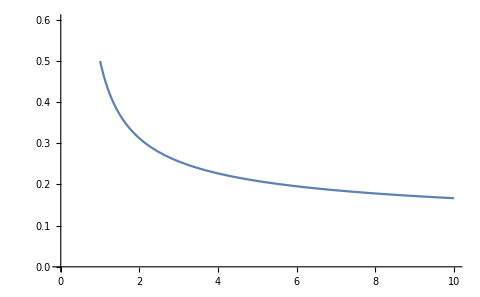

```mathematica
Plot[(1/(2(1+2 Log10[l]))),{l,1,10},PlotRange->{{0,10},{0,0.6}}]
```

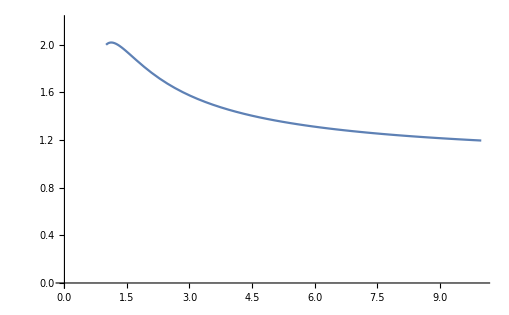

```mathematica
Plot[(1/(2(1+2 Log10[l])))^(-1/l),{l,1,10}, PlotRange->{{0,10},{0,2.2}}]
```

```mathematica
{{{, {{0, x≤a}, {⌊log(x)⌋+1, a<x≤1}, {⌊llog(w)+log(ax)⌋+l+1, 1<x≤1}, {2l+1, x>1}}}}
```

```mathematica
{{{, {{0, x≤a}, {⌊log(x)⌋+1, a<x≤1}, {⌊llog(w)+log(ax)⌋+l+1, 1<x≤1}, {2l+1, x>1}}}}
```

```mathematica
{{{, {{0, x≤a}, {⌊log(x)⌋+1, a<x≤1}, {⌊llog(w)+log(ax)⌋+l+1, 1<x≤1}, {2l+1, x>1}}}}
```

```mathematica
Piecewise[{{0,x≤ a},{1 + Floor[Log10[x/a]/Log10[w]],a<x≤ 1},{l +1 + Floor[(Log10[a x] + (l* Log10[w]))/Log10[w]],1<x≤ 1/a},{2 l + 1,x>1/a}}]
```

```mathematica
\begin{array}{cc}
 \{&\begin{array}{cc} 0& x\leq a \\\left\lfloor\frac{\log _{10}\left(\frac{x}{a}\right)}{\log _{10}(w)}\right\rfloor+1& a<x\leq 1 \\\left\lfloor\frac{l\log _{10}(w)+\log _{10}(a x)}{\log _{10}(w)}\right\rfloor+l+1& 1<x\leq\frac{1}{a} \\ 2 l+1& x>\frac{1}{a} \\\end{array} \\\end{array}
```